## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.5; qscal=0.7; Q=0.948;
```

```mathematica
winit=(0.45-0.00005*I)
```

0.45-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

0.515488-2.81211×10^-10 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=rp+10^(-8);r1=45; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.498466

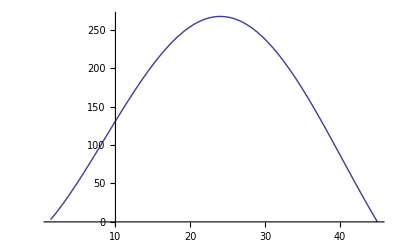

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.45+0.000005*I);
ie=0;While[ie<301,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,300}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,300}]
```

NDSolve::ndsz: At r == 1.31827, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {45} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At r == 1.31827, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {45} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

$Aborted

{{45.,-0.680937},{45.2,-0.680937},{45.4,-0.680937},{45.6,-0.680937},{45.8,-0.680937},{46.,-0.680937},{46.2,-0.680937},{46.4,-0.680937},{46.6,-0.680937},{46.8,-0.680937},{47.,-0.680937},{47.2,-0.680937},{47.4,-0.680937},{47.6,-0.680937},{47.8,-0.680937},{48.,-0.680937},{48.2,-0.680937},{48.4,-0.680937},{48.6,-0.680937},{48.8,-0.680937},{49.,-0.680937},{49.2,-0.680937},{49.4,-0.680937},{49.6,-0.680937},{49.8,-0.680937},{50.,-0.680937},{50.2,-0.680937},{50.4,-0.680937},{50.6,-0.680937},{50.8,-0.680937},{51.,-0.680937},{51.2,-0.680937},{51.4,-0.680937},{51.6,-0.680937},{51.8,-0.680937},{52.,-0.680937},{52.2,-0.680937},{52.4,-0.680937},{52.6,-0.680937},{52.8,-0.680937},{53.,-0.680937},{53.2,-0.680937},{53.4,-0.680937},{53.6,-0.680937},{53.8,-0.680937},{54.,-0.680937},{54.2,-0.680937},{54.4,-0.680937},{54.6,-0.680937},{54.8,-0.680937},{55.,-0.680937},{55.2,-0.680937},{55.4,-0.680937},{55.6,-0.680937},{55.8,-1.98598×10^-11},{56.,-1.91785×10^-11},{56.2,-1.8521×10^-11},{56.4,-1.78874×10^-11},{56.6,-1.69158×10^-11},{56.8,-1.66878×10^-11},{57.,-1.6154×10^-11},{57.2,-1.55709×10^-11},{57.4,-1.5045×10^-11},{57.6,-1.45361×10^-11},{57.8,-1.4045×10^-11},{58.,-1.42762×10^-11},{58.2,-1.31148×10^-11},{58.4,-1.36378×10^-11},{58.6,-1.2249×10^-11},{58.8,-1.19114×10^-11},{59.,-1.14431×10^-11},{59.2,-1.10609×10^-11},{59.4,-1.06922×10^-11},{59.6,-1.03364×10^-11},{59.8,-1.39997×10^-11},{60.,-9.66143×10^-12},{60.2,-9.34181×10^-12},{60.4,-9.03306×10^-12},{60.6,-2.73654×10^-12},{60.8,-9.1473×10^-12},{61.,-8.16732×10^-12},{61.2,-7.89994×10^-12},{61.4,-7.63877×10^-12},{61.6,-7.38791×10^-12},{61.8,-8.09727×10^-12},{62.,-6.91323×10^-12},{62.2,-6.68594×10^-12},{62.4,-6.46343×10^-12},{62.6,-6.25684×10^-12},{62.8,-6.05293×10^-12},{63.,-5.85589×10^-12},{63.2,-5.66556×10^-12},{63.4,-5.23056×10^-12},{63.6,-5.30413×10^-12},{63.8,-5.13163×10^-12},{64.,-4.96558×10^-12},{64.2,-4.80493×10^-12},{64.4,-4.64964×10^-12},{64.6,-4.49944×10^-12},{64.8,-3.19276×10^-12},{65.,-4.21396×10^-12},{65.2,-4.07834×10^-12},{65.4,-3.94698×10^-12},{65.6,-3.82001×10^-12},{65.8,-3.69717×10^-12},{66.,-3.57852×10^-12},{66.2,-3.4638×10^-12},{66.4,-3.35248×10^-12},{66.6,-3.24501×10^-12},{66.8,-3.14228×10^-12},{67.,-3.04084×10^-12},{67.2,-2.74959×10^-12},{67.4,-2.84913×10^-12},{67.6,-2.94442×10^-12},{67.8,-2.66994×10^-12},{68.,-2.58447×10^-12},{68.2,-2.50201×10^-12},{68.4,-2.42213×10^-12},{68.6,-2.34475×10^-12},{68.8,-2.27008×10^-12},{69.,-2.19761×10^-12},{69.2,-2.12737×10^-12},{69.4,-2.05961×10^-12},{69.6,-1.99393×10^-12},{69.8,-1.93036×10^-12},{70.,-1.86883×10^-12},{70.2,-1.80918×10^-12},{70.4,-1.75113×10^-12},{70.6,-1.69561×10^-12},{70.8,-1.64153×10^-12},{71.,-1.58914×10^-12},{71.2,-1.53798×10^-12},{71.4,-1.48931×10^-12},{71.6,-1.74734×10^-12},{71.8,-1.39572×10^-12},{72.,-2.04251×10^-12},{72.2,-1.30805×10^-12},{72.4,-1.2671×10^-12},{72.6,-1.22561×10^-12},{72.8,-1.18637×10^-12},{73.,-1.15113×10^-12},{73.2,-1.11152×10^-12},{73.4,-1.0758×10^-12},{73.6,-1.04045×10^-12},{73.8,-1.00788×10^-12},{74.,-9.75349×10^-13},{74.2,-9.44057×10^-13},{74.4,-9.12932×10^-13},{74.6,-8.84175×10^-13},{74.8,-8.58275×10^-13},{75.,-8.276×10^-13},{75.2,-8.01186×10^-13},{75.4,-7.75021×10^-13},{75.6,-7.50069×10^-13},{75.8,-7.25676×10^-13},{76.,-7.02081×10^-13},{76.2,-6.7918×10^-13},{76.4,-6.56994×10^-13},{76.6,-1.99409×10^-12},{76.8,-6.11146×10^-13},{77.,-5.95742×10^-13},{77.2,-5.75099×10^-13},{77.4,-5.56069×10^-13},{77.6,-5.37682×10^-13},{77.8,-5.19848×10^-13},{78.,-5.0269×10^-13},{78.2,-1.4752×10^-12},{78.4,-4.69812×10^-13},{78.6,-4.54117×10^-13},{78.8,-4.38936×10^-13},{79.,-4.28321×10^-13},{79.2,-4.0994×10^-13},{79.4,-3.96108×10^-13},{79.6,-3.82728×10^-13},{79.8,-3.69721×10^-13},{80.,-3.57129×10^-13},{80.2,-3.44937×10^-13},{80.4,-3.33105×10^-13},{80.6,-2.90106×10^-13},{80.8,-3.26932×10^-13},{81.,-2.99811×10^-13},{81.2,-3.05486×10^-13},{81.4,-2.79289×10^-13},{81.6,-1.16921×10^-12},{81.8,-2.60018×10^-13},{82.,-5.97243×10^-13},{82.2,-2.44787×10^-13},{82.4,-2.33329×10^-13},{82.6,-2.23178×10^-13},{82.8,-2.16848×10^-13},{83.,-3.7024×10^-12},{83.2,-2.01391×10^-13},{83.4,-2.11525×10^-13},{83.6,-1.8687×10^-13},{83.8,-1.79951×10^-13},{84.,-1.73249×10^-13},{84.2,-1.36754×10^-13},{84.4,-1.66436×10^-13},{84.6,-1.54005×10^-13},{84.8,-1.48476×10^-13},{85.,-1.42767×10^-13},{85.2,-1.37231×10^-13},{85.4,-1.32276×10^-13},{85.6,-1.26668×10^-13},{85.8,-1.21625×10^-13},{86.,-1.16763×10^-13},{86.2,-1.67896×10^-13},{86.4,-1.0745×10^-13},{86.6,-1.03052×10^-13},{86.8,-9.87586×10^-14},{87.,-9.46165×10^-14},{87.2,-9.24644×10^-14},{87.4,-8.67056×10^-14},{87.6,-8.29354×10^-14},{87.8,-8.60795×10^-14},{88.,-1.33807×10^-13},{88.2,-7.23442×10^-14},{88.4,-6.91249×10^-14},{88.6,-7.26612×10^-14},{88.8,-6.27468×10^-14},{89.,-8.02106×10^-14},{89.2,-5.68545×10^-14},{89.4,-5.40488×10^-14},{89.6,-7.52166×10^-14},{89.8,-5.74725×10^-14},{90.,-4.61578×10^-14},{90.2,-4.37197×10^-14},{90.4,-4.13401×10^-14},{90.6,-3.90422×10^-14},{90.8,-4.92691×10^-14},{91.,-3.59991×10^-14},{91.2,-3.26065×10^-14},{91.4,-3.06036×10^-14},{91.6,-2.86489×10^-14},{91.8,-2.67927×10^-14},{92.,8.90105×10^-15},{92.2,-2.31721×10^-14},{92.4,9.20522×10^-14},{92.6,-1.99134×10^-14},{92.8,-1.83368×10^-14},{93.,-4.08105×10^-14},{93.2,-1.53483×10^-14},{93.4,-1.39421×10^-14},{93.6,3.85809×10^-16},{93.8,-1.1245×10^-14},{94.,-7.75804×10^-15},{94.2,-8.73935×10^-15},{94.4,-7.55706×10^-15},{94.6,-6.41599×10^-15},{94.8,-5.31639×10^-15},{95.,-4.25654×10^-15},{95.2,-3.23645×10^-15},{95.4,-5.26708×10^-15},{95.6,-1.30341×10^-15},{95.8,-4.17532×10^-15},{96.,7.41891×10^-15},{96.2,-1.40297×10^-14},{96.4,2.13222×10^-15},{96.6,2.92698×10^-15},{96.8,3.67896×10^-15},{97.,4.45634×10^-15},{97.2,5.10168×10^-15},{97.4,5.76174×10^-15},{97.6,6.40452×10^-15},{97.8,7.02256×10^-15},{98.,1.06812×10^-13},{98.2,-1.07268×10^-13},{98.4,1.41237×10^-14},{98.6,9.25245×10^-15},{98.8,9.73642×10^-15},{99.,1.02129×10^-14},{99.2,1.06691×10^-14},{99.4,-9.31974×10^-13},{99.6,1.15243×10^-14},{99.8,-1.6056×10^-13},{100.,4.3158×10^-14},{100.2,2.69853×10^-13},{100.4,1.30042×10^-14},{100.6,1.33352×10^-14},{100.8,1.36334×10^-14},{101.,1.39443×10^-14},{101.2,1.41785×10^-14},{101.4,1.44629×10^-14},{101.6,6.24891×10^-15},{101.8,1.49881×10^-14},{102.,1.49308×10^-14},{102.2,-4.8991×10^-14},{102.4,1.56283×10^-14},{102.6,-7.65906×10^-16},{102.8,1.60041×10^-14},{103.,1.60897×10^-14},{103.2,1.63258×10^-14},{103.4,1.6473×10^-14},{103.6,1.65083×10^-14},{103.8,-3.94267×10^-14},{104.,4.17525×10^-14},{104.2,1.69587×10^-14},{104.4,1.70612×10^-14},{104.6,9.41469×10^-14},{104.8,1.72387×10^-14},{105.,1.73107×10^-14}}

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.4+0.000005*I);
ie=0;While[ie<176,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,175}];
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,175}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*The imaginary part vs the radius*)
```

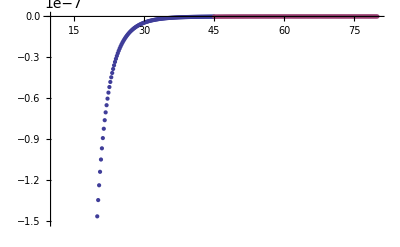

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

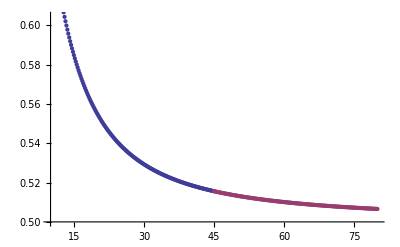

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.4/Q=0.950/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.4/Q=0.950/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.4/Q=0.950/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.4/Q=0.950/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-Q^2]
rm=M-Sqrt[M^2-Q^2]
rmirror=40
```

1.6

0.4

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*Q/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.45

2.13333 (-0.45+wa)

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```